## Function definition

```mathematica
Clear[ODistance]
```

```mathematica
Clear[ODistanceSq]
```

```mathematica
ODistance[OPoint[x_,y_],OPoint[u_,v_]]:=√((x-u)^2+(y-v)^2)
```

```mathematica
ODistanceSq[OPoint[x_,y_],OPoint[u_,v_]]:=(x-u)^2+(y-v)^2
```

```mathematica
ODistance[OPoint[x_,y_],OLine[a_,b_,c_]]:=Abs[a x+b y+ c]/(√(a^2+b^2))
```

```mathematica
ODistanceSq[OPoint[x_,y_],OLine[a_,b_,c_]]:=(a x+b y+ c)^2/(a^2+b^2)
```

```mathematica
ODistanceSq[OLine[a_,b_,c1_],OLine[a_,b_,c2_]]:=(c1-c2)^2/(a^2+b^2)
```

```mathematica
OMidPoint[OPoint[x1_,y1_],OPoint[x2_,y2_]]:= OPoint[(x1+y1)/2,(x2+y2)/2]
```

## Proof where lines m and n are perpendicular

(O6) The fold that brings P onto m and Q onto n.

All parabola are similar. Without loss of generalization, take two perpendiculat lines m and n.

```mathematica
P=OPoint[p1,p2];Q=OPoint[q1,q2];
```

```mathematica
m=OLine[1,0,cm];n=OLine[0,1,cn];
```

Equation of parabola (P, m)

```mathematica
parabolaeq1=ODistance[OPoint[x,y],P]^2-ODistanceSq[OPoint[x,y],m]
```

-(cm+x)^2+(-p1+x)^2+(-p2+y)^2

Equation of parabola (Q, n)

```mathematica
parabolaeq2=ODistance[OPoint[x,y],Q]^2-ODistanceSq[OPoint[x,y],n]
```

(-q1+x)^2-(cn+y)^2+(-q2+y)^2

The equation of a tangent to parabola (P, m) and passing through point S(x1,y1)

```mathematica
tgparabola1=(D[parabolaeq1,x]/.{x-> x1, y-> y1})+ (D[parabolaeq1,y]/.{x-> x1, y-> y1})t
```

-2 (cm+x1)+2 (-p1+x1)+2 t (-p2+y1)

The equation of a tangent to parabola (Q, n) and passing through point T(x2,y2)

```mathematica
tgparabola2=(D[parabolaeq2,x]/.{x-> x2, y-> y2})+ (D[parabolaeq2,y]/.{x-> x2, y-> y2})t
```

2 (-q1+x2)+t (-2 (cn+y2)+2 (-q2+y2))

Since the solution is common tangent to two parabolas, then tgparabola1 should also pass through T(x2, y2) and tgparabola2 should pass through S(x1,y1).

```mathematica
cst1=tgparabola1/.{x-> x2,y-> y2}
```

-2 (cm+x1)+2 (-p1+x1)+2 t (-p2+y1)

```mathematica
cst2=tgparabola2/.{x-> x1,y-> y1}
```

2 (-q1+x2)+t (-2 (cn+y2)+2 (-q2+y2))

S(x1,y1) is a point of  parabola (P, m)

```mathematica
cst3=parabolaeq1/.{x-> x1,y-> y1}
```

-(cm+x1)^2+(-p1+x1)^2+(-p2+y1)^2

T(x2,y2) is a point of  parabola (Q, n)

```mathematica
cst4=parabolaeq2/.{x-> x2,y-> y2}
```

(-q1+x2)^2-(cn+y2)^2+(-q2+y2)^2

Let t be the slope of the common tangent.

```mathematica
cst5=(y1-y2)-t(x1-x2)
```

-t (x1-x2)+y1-y2

We compute the GroebnerBasis of the constraints. We add two more equations to exclude degenerate cases (infinite solutions) or special cases (reduce (O6) to simpler operations) (Ghourabi et. al., 2013). We eliminate some of the variables and obtain a cubic polynomial in t^3. The polynomials cst1, cst2, cst3, cst4, cst5 have common roots that are solutions of the cubic equation cn+q1+(cm-p2+2 q2) t+(cn+2 p1-q1) t^2+(cm+p2) t^3.

```mathematica
gbx1=GroebnerBasis[{cst1==0,cst2==0,cst3== 0,cst4== 0,cst5== 0,η1 (cn+q2)-1== 0,η2(cm+p1)-1== 0},{t},{x1,x2,y1,y2,η1,η2}]//FullSimplify
```

{cm+p1+(cn+2 p2-q2) t+(cm-p1+2 q1) t^2+(cn+q2) t^3}

```mathematica
(* Discriminant[a x^3+b x^2+c x+ e,x]*)
```

```mathematica
(* b^2 c^2-4 a c^3-4 b^3 e+18 a b c e-27 a^2 e^2*)
```

```mathematica
gb=cm+p1+(cn+2 p2-q2) t+(cm-p1+2 q1) t^2+(cn+q2) t^3/.{p1-> 3,p2-> 4,cm-> 0,cn-> 0}
```

3+(8-q2) t+(-3+2 q1) t^2+q2 t^3

The discriminant (or resultant?) can hint on the number of the solutions. Here, we fix P, m, and m. We obtain a polynomial expresion on q1 and q2.

```mathematica
d=Discriminant[gbx1[[1]]/.{p1-> 3,p2-> 4,cm-> 0,cn-> 0},t]//FullSimplify
```

4 (-(3-2 q1)^2 (-25+6 q1)-8 (109+q1 (-33+2 q1)) q2+(174+(-30+q1) q1) q2^2-24 q2^3+q2^4)

```mathematica
Solve[d== 0,{q2},Reals]
```

{{q2→ConditionalExpression[Root[225-354 q1+172 q1^2-24 q1^3+(-872+264 q1-16 q1^2) #1+(174-30 q1+q1^2) #1^2-24 #1^3+#1^4&,1],-4<q1<4||4<q1<3/2 (-5+3^(1/3)+3 3^(2/3))||q1>3/2 (-5+3^(1/3)+3 3^(2/3))]},{q2→ConditionalExpression[Root[225-354 q1+172 q1^2-24 q1^3+(-872+264 q1-16 q1^2) #1+(174-30 q1+q1^2) #1^2-24 #1^3+#1^4&,2],-4<q1<4||4<q1<3/2 (-5+3^(1/3)+3 3^(2/3))||q1>3/2 (-5+3^(1/3)+3 3^(2/3))]},{q2→ConditionalExpression[Root[225-354 q1+172 q1^2-24 q1^3+(-872+264 q1-16 q1^2) #1+(174-30 q1+q1^2) #1^2-24 #1^3+#1^4&,3],4<q1<3/2 (-5+3^(1/3)+3 3^(2/3))]},{q2→ConditionalExpression[Root[225-354 q1+172 q1^2-24 q1^3+(-872+264 q1-16 q1^2) #1+(174-30 q1+q1^2) #1^2-24 #1^3+#1^4&,4],4<q1<3/2 (-5+3^(1/3)+3 3^(2/3))]}}

```mathematica
CylindricalDecomposition[d>0,{q1,q2}]
```

q1<-4||(-4≤q1<4&&(q2<Root[225-354 q1+172 q1^2-24 q1^3+(-872+264 q1-16 q1^2) #1+(174-30 q1+q1^2) #1^2-24 #1^3+#1^4&,1]||q2>Root[225-354 q1+172 q1^2-24 q1^3+(-872+264 q1-16 q1^2) #1+(174-30 q1+q1^2) #1^2-24 #1^3+#1^4&,2]))||(4≤q1<Root[-1728+216 #1+45 #1^2+2 #1^3&,1]&&(q2<Root[225-354 q1+172 q1^2-24 q1^3+(-872+264 q1-16 q1^2) #1+(174-30 q1+q1^2) #1^2-24 #1^3+#1^4&,1]||Root[225-354 q1+172 q1^2-24 q1^3+(-872+264 q1-16 q1^2) #1+(174-30 q1+q1^2) #1^2-24 #1^3+#1^4&,2]<q2<Root[225-354 q1+172 q1^2-24 q1^3+(-872+264 q1-16 q1^2) #1+(174-30 q1+q1^2) #1^2-24 #1^3+#1^4&,3]||q2>Root[225-354 q1+172 q1^2-24 q1^3+(-872+264 q1-16 q1^2) #1+(174-30 q1+q1^2) #1^2-24 #1^3+#1^4&,4]))||(q1==Root[-1728+216 #1+45 #1^2+2 #1^3&,1]&&(q2<Root[225-354 q1+172 q1^2-24 q1^3+(-872+264 q1-16 q1^2) #1+(174-30 q1+q1^2) #1^2-24 #1^3+#1^4&,1]||q2>Root[225-354 q1+172 q1^2-24 q1^3+(-872+264 q1-16 q1^2) #1+(174-30 q1+q1^2) #1^2-24 #1^3+#1^4&,4]))||(q1>Root[-1728+216 #1+45 #1^2+2 #1^3&,1]&&(q2<Root[225-354 q1+172 q1^2-24 q1^3+(-872+264 q1-16 q1^2) #1+(174-30 q1+q1^2) #1^2-24 #1^3+#1^4&,1]||q2>Root[225-354 q1+172 q1^2-24 q1^3+(-872+264 q1-16 q1^2) #1+(174-30 q1+q1^2) #1^2-24 #1^3+#1^4&,2]))

We finally plot the discriminat, i.e. q2 = f (q1).

d = 0, the cubic has a real root of multiplicity > 1 and all the roots are reals. 1 root of multiplicity 2 and 1 single root, or 1 root of multiplicity 3. The cusp means 1 single real root of multiplicity 3??

d>0, the cubic has three distinct real roots.

d<0, the cubic has 1 real root and two complex conjugate roots.

3+(8-q2) t+(-3+2 q1) t^2+q2 t^3

```mathematica
d0=(-3+2q1)^2-3q2(8-q2)
```

(-3+2 q1)^2-3 (8-q2) q2

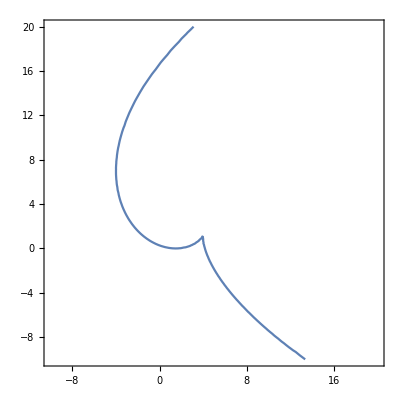

```mathematica
ContourPlot[d==0,{q1,-10,20},{q2,-10,20}]
```

```mathematica
d0
```

(-3+2 q1)^2-3 (8-q2) q2

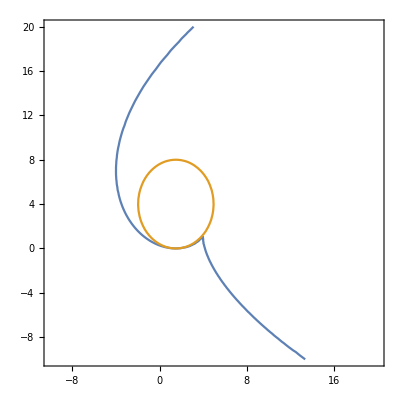

```mathematica
ContourPlot[{d== 0,d0==  0},{q1,-10,20},{q2,-10,20}]
```

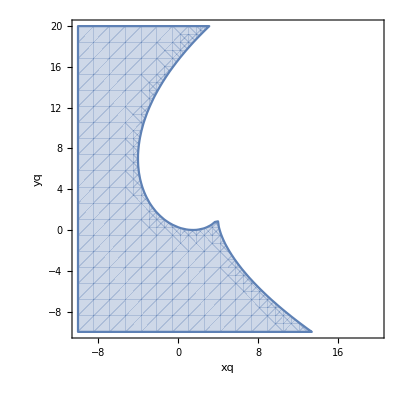

```mathematica
RegionPlot[d> 0,{q1,-10,20},{q2,-10,20},AxesLabel-> {xq,yq}]
```

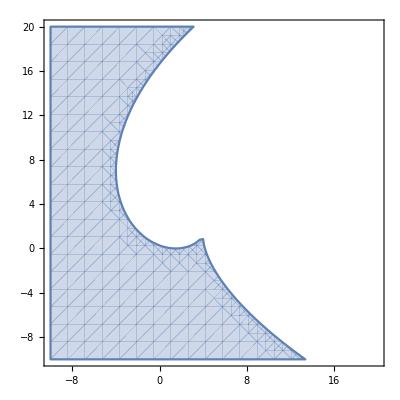

```mathematica
Graphics[RegionPlot[{d> 0},{q1,-10,20},{q2,-10,20}],AxesLabel-> {xq,yq}]
```

```mathematica
d//FullSimplify
```

4 (-(3-2 q1)^2 (-25+6 q1)-8 (109+q1 (-33+2 q1)) q2+(174+(-30+q1) q1) q2^2-24 q2^3+q2^4)

```mathematica
Factor[4 (-(3-2 q1)^2 (-25+6 q1)-8 (109+q1 (-33+2 q1)) q2+(174+(-30+q1) q1) q2^2-24 q2^3+q2^4)]
```

-4 (-225+354 q1-172 q1^2+24 q1^3+872 q2-264 q1 q2+16 q1^2 q2-174 q2^2+30 q1 q2^2-q1^2 q2^2+24 q2^3-q2^4)

```mathematica
D[d,q1](q1-X)+D[d,q2](q2-Y)
```

4 (-6 (3-2 q1)^2+4 (3-2 q1) (-25+6 q1)-8 (-33+4 q1) q2+(-30+2 q1) q2^2) (q1-X)+4 (-8 (109+q1 (-33+2 q1))+2 (174+(-30+q1) q1) q2-72 q2^2+4 q2^3) (q2-Y)

## Tests

### Test 1 - one fold line, Q above the locus curve

```mathematica
p1=1.19y^2-52.61x-10.6y+1024
```

1024-52.61 x-10.6 y+1.19 y^2

```mathematica
p2=1.01x^2-64.72y+256
```

256+1.01 x^2-64.72 y

```mathematica
tgp1=(D[p1,x]/.{x-> x1, y-> y1})+ (D[p1,y]/.{x-> x1, y-> y1})t
```

-52.61+t (-10.6+2.38 y1)

```mathematica
tgp2=(D[p2,x]/.{x-> x2, y-> y2})+ (D[p2,y]/.{x-> x2, y-> y2})t
```

-64.72 t+2.02 x2

```mathematica
gb=GroebnerBasis[{p1/.{x-> x1,y-> y1},p2/.{x-> x2, y-> y2}, tgp1,tgp2,(y1-y2)-(x1-x2)t},{t},{x1,x2,y1,y2}]
```

{0.689929+0.0311041 t-1.18699 t^2+1. t^3}

```mathematica
Solve[gb[[1]]== 0,t]
```

{{t→-0.610884},{t→0.898936-0.566841 ⅈ},{t→0.898936+0.566841 ⅈ}}

### Test 2 - two fold lines, Q on the locus curve

```mathematica
P=OPoint[3,4];Q=OPoint[q1,q2];
```

```mathematica
m=OLine[1,0,0];n=OLine[0,1,0];
```

```mathematica
parabolaeq1=ODistance[OPoint[x,y],P]^2-ODistanceSq[OPoint[x,y],m]//Expand
```

25-6 x-8 y+y^2

```mathematica
parabolaeq2=ODistance[OPoint[x,y],Q]^2-ODistanceSq[OPoint[x,y],n]
```

(-q1+x)^2-y^2+(-q2+y)^2

```mathematica
tgparabola1=(D[parabolaeq1,x]/.{x-> x1, y-> y1})+ (D[parabolaeq1,y]/.{x-> x1, y-> y1})t
```

-6+t (-8+2 y1)

```mathematica
tgparabola2=(D[parabolaeq2,x]/.{x-> x2, y-> y2})+ (D[parabolaeq2,y]/.{x-> x2, y-> y2})t
```

2 (-q1+x2)+t (-2 y2+2 (-q2+y2))

```mathematica
cst1=tgparabola1/.{x-> x2,y-> y2}
```

-6+t (-8+2 y1)

```mathematica
cst2=tgparabola2/.{x-> x1,y-> y1}
```

2 (-q1+x2)+t (-2 y2+2 (-q2+y2))

```mathematica
cst3=parabolaeq1/.{x-> x1,y-> y1}
```

25-6 x1-8 y1+y1^2

```mathematica
cst4=parabolaeq2/.{x-> x2,y-> y2}
```

(-q1+x2)^2-y2^2+(-q2+y2)^2

```mathematica
cst5=(y1-y2)-t(x1-x2)
```

-t (x1-x2)+y1-y2

We compute the GroebnerBasis of the constraints. We add two more equations to exclude degenerate cases (infinite solutions) or special cases (reduce (O6) to simpler operations) (Ghourabi et. al., 2013). We eliminate some of the variables and obtain a cubic polynomial in t^3. The polynomials cst1, cst2, cst3, cst4, cst5 have common roots that are solutions of the cubic equation cn+q1+(cm-p2+2 q2) t+(cn+2 p1-q1) t^2+(cm+p2) t^3.

```mathematica
gb=GroebnerBasis[{cst1==0,cst2==0,cst3== 0,cst4== 0,cst5== 0},{t},{x1,x2,y1,y2}]
```

{3 q2+8 q2 t-q2^2 t-3 q2 t^2+2 q1 q2 t^2+q2^2 t^3}

```mathematica
Collect[gb[[1]],{t,t^2,t^3}]
```

3 q2+(8 q2-q2^2) t+(-3 q2+2 q1 q2) t^2+q2^2 t^3

```mathematica
d=Discriminant[gb[[1]],t]//FullSimplify
```

4 q2^4 (-(3-2 q1)^2 (-25+6 q1)-8 (109+q1 (-33+2 q1)) q2+(174+(-30+q1) q1) q2^2-24 q2^3+q2^4)

```mathematica
d0=(-3 q2+2 q1 q2)^2-3 q2^2(8 q2-q2^2)//FullSimplify
```

q2^2 (4 (-3+q1) q1+3 (3+(-8+q2) q2))

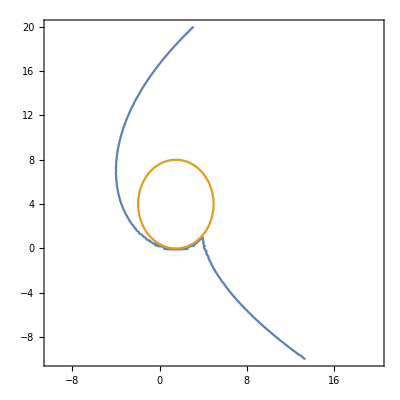

```mathematica
ContourPlot[{d==0,(4 (-3+q1) q1+3 (3+(-8+q2) q2))==0},{q1,-10,20},{q2,-10,20}]
```

```mathematica
Solve[{d==0,d0==0},{q1,q2}]//N
```

{{q2→0.},{q1→1.5,q2→0.},{q1→4.02375,q2→1.26001},{q1→-13.2619+6.23279 ⅈ,q2→11.37+16.6454 ⅈ},{q1→-13.2619-6.23279 ⅈ,q2→11.37-16.6454 ⅈ}}

#### Example 1 : Q (0, q2)

```mathematica
{Solve[d== 0/.{q1-> 0},q2]//N,Solve[d== 0/.{q1-> 0},q2]}
```

{{{q2→0.},{q2→0.},{q2→0.},{q2→0.},{q2→3.54137-6.09149 ⅈ},{q2→3.54137+6.09149 ⅈ},{q2→0.272271},{q2→16.645}},{{q2→0},{q2→0},{q2→0},{q2→0},{q2→6-√(7-69/(-11+64 √3)^(1/3)+3 (-11+64 √3)^(1/3))-1/2 √(56+276/(-11+64 √3)^(1/3)-12 (-11+64 √3)^(1/3)-512/(√(7-69/(-11+64 √3)^(1/3)+3 (-11+64 √3)^(1/3))))},{q2→6-√(7-69/(-11+64 √3)^(1/3)+3 (-11+64 √3)^(1/3))+1/2 √(56+276/(-11+64 √3)^(1/3)-12 (-11+64 √3)^(1/3)-512/(√(7-69/(-11+64 √3)^(1/3)+3 (-11+64 √3)^(1/3))))},{q2→6+√(7-69/(-11+64 √3)^(1/3)+3 (-11+64 √3)^(1/3))-1/2 √(56+276/(-11+64 √3)^(1/3)-12 (-11+64 √3)^(1/3)+512/(√(7-69/(-11+64 √3)^(1/3)+3 (-11+64 √3)^(1/3))))},{q2→6+√(7-69/(-11+64 √3)^(1/3)+3 (-11+64 √3)^(1/3))+1/2 √(56+276/(-11+64 √3)^(1/3)-12 (-11+64 √3)^(1/3)+512/(√(7-69/(-11+64 √3)^(1/3)+3 (-11+64 √3)^(1/3))))}}}

```mathematica
q={q1-> 0,q2-> 6+√(7-69/(-11+64 √3)^(1/3)+3 (-11+64 √3)^(1/3))-1/2 √(56+276/(-11+64 √3)^(1/3)-12 (-11+64 √3)^(1/3)+512/(√(7-69/(-11+64 √3)^(1/3)+3 (-11+64 √3)^(1/3))))}
```

{q1→0,q2→6+√(7-69/(-11+64 √3)^(1/3)+3 (-11+64 √3)^(1/3))-1/2 √(56+276/(-11+64 √3)^(1/3)-12 (-11+64 √3)^(1/3)+512/(√(7-69/(-11+64 √3)^(1/3)+3 (-11+64 √3)^(1/3))))}

```mathematica
d/.q//N
```

1.38289×10^-14

```mathematica
NSolve[(gb[[1]]== 0)/.q,t,Reals]
```

{{t→-0.341527}}

1 single real root and 1 real double root

```mathematica
NSolve[(gb[[1]]== 0)/.q,t]//Chop
```

{{t→-0.341527},{t→5.67999-3.08047×10^-6 ⅈ},{t→5.67999+3.08047×10^-6 ⅈ}}

#### Example 2 : Q (10, q2)

```mathematica
{Solve[d== 0/.{q1->10},q2]//N,Solve[d== 0/.{q1->10},q2]}
```

{{{q2→0.},{q2→0.},{q2→0.},{q2→0.},{q2→3.0147-6.68433 ⅈ},{q2→3.0147+6.68433 ⅈ},{q2→-7.41154},{q2→25.3821}},{{q2→0},{q2→0},{q2→0},{q2→0},{q2→6-1/(√(6/(242-13576 (2/(-2757193+15597 √36393))^(1/3)+2^(2/3) (-2757193+15597 √36393)^(1/3))))-1/2 √(968/3+27152/3 (2/(-2757193+15597 √36393))^(1/3)-2/3 2^(2/3) (-2757193+15597 √36393)^(1/3)-1872 √(6/(242-13576 (2/(-2757193+15597 √36393))^(1/3)+2^(2/3) (-2757193+15597 √36393)^(1/3))))},{q2→6-1/(√(6/(242-13576 (2/(-2757193+15597 √36393))^(1/3)+2^(2/3) (-2757193+15597 √36393)^(1/3))))+1/2 √(968/3+27152/3 (2/(-2757193+15597 √36393))^(1/3)-2/3 2^(2/3) (-2757193+15597 √36393)^(1/3)-1872 √(6/(242-13576 (2/(-2757193+15597 √36393))^(1/3)+2^(2/3) (-2757193+15597 √36393)^(1/3))))},{q2→6+1/(√(6/(242-13576 (2/(-2757193+15597 √36393))^(1/3)+2^(2/3) (-2757193+15597 √36393)^(1/3))))-1/2 √(968/3+27152/3 (2/(-2757193+15597 √36393))^(1/3)-2/3 2^(2/3) (-2757193+15597 √36393)^(1/3)+1872 √(6/(242-13576 (2/(-2757193+15597 √36393))^(1/3)+2^(2/3) (-2757193+15597 √36393)^(1/3))))},{q2→6+1/(√(6/(242-13576 (2/(-2757193+15597 √36393))^(1/3)+2^(2/3) (-2757193+15597 √36393)^(1/3))))+1/2 √(968/3+27152/3 (2/(-2757193+15597 √36393))^(1/3)-2/3 2^(2/3) (-2757193+15597 √36393)^(1/3)+1872 √(6/(242-13576 (2/(-2757193+15597 √36393))^(1/3)+2^(2/3) (-2757193+15597 √36393)^(1/3))))}}}

```mathematica
q={q1-> 10,q2-> 6+1/(√(6/(242-13576 (2/(-2757193+15597 √36393))^(1/3)+2^(2/3) (-2757193+15597 √36393)^(1/3))))-1/2 √(968/3+27152/3 (2/(-2757193+15597 √36393))^(1/3)-2/3 2^(2/3) (-2757193+15597 √36393)^(1/3)+1872 √(6/(242-13576 (2/(-2757193+15597 √36393))^(1/3)+2^(2/3) (-2757193+15597 √36393)^(1/3))))}
```

{q1→10,q2→6+1/(√(6/(242-13576 (2/(-2757193+15597 √36393))^(1/3)+2^(2/3) (-2757193+15597 √36393)^(1/3))))-1/2 √(968/3+27152/3 (2/(-2757193+15597 √36393))^(1/3)-2/3 2^(2/3) (-2757193+15597 √36393)^(1/3)+1872 √(6/(242-13576 (2/(-2757193+15597 √36393))^(1/3)+2^(2/3) (-2757193+15597 √36393)^(1/3))))}

```mathematica
d/.q//N
```

1.75636×10^-7

1 single real root and 1 real double root

```mathematica
NSolve[(gb[[1]]== 0)/.q,t]
```

{{t→-0.365783},{t→-0.365783},{t→3.02529}}

### Test 3 - Q is the cusp, one real triple root

```mathematica
Solve[{d==0,d0==0},{q1,q2}]//N
```

{{q2→0.},{q1→1.5,q2→0.},{q1→4.02375,q2→1.26001},{q1→-13.2619+6.23279 ⅈ,q2→11.37+16.6454 ⅈ},{q1→-13.2619-6.23279 ⅈ,q2→11.37-16.6454 ⅈ}}

```mathematica
NSolve[(gb[[1]]==0)/.{q1->4.0237515591946815,q2->1.2600053363890371},t]
```

{{t→-1.33531},{t→-1.33531},{t→-1.33531}}

In the case of {q1 -> 1.5`, q2 -> 0.`}, we have Q is on n which is an incidence case ((O6) is reduced to simpler operations)

```mathematica
gb[[1]]/.{q1-> 3/2,q2-> 0}
```

0

### Test 4 - three distinct fold lines, Q below the locus curve

```mathematica
P=OPoint[3,4];Q=OPoint[q1,q2];
```

```mathematica
m=OLine[1,0,0];n=OLine[0,1,0];
```

```mathematica
parabolaeq1=ODistance[OPoint[x,y],P]^2-ODistanceSq[OPoint[x,y],m]//Expand
```

25-6 x-8 y+y^2

```mathematica
parabolaeq2=ODistance[OPoint[x,y],Q]^2-ODistanceSq[OPoint[x,y],n]
```

(-q1+x)^2-y^2+(-q2+y)^2

```mathematica
tgparabola1=(D[parabolaeq1,x]/.{x-> x1, y-> y1})+ (D[parabolaeq1,y]/.{x-> x1, y-> y1})t
```

-6+t (-8+2 y1)

```mathematica
tgparabola2=(D[parabolaeq2,x]/.{x-> x2, y-> y2})+ (D[parabolaeq2,y]/.{x-> x2, y-> y2})t
```

2 (-q1+x2)+t (-2 y2+2 (-q2+y2))

```mathematica
cst1=tgparabola1/.{x-> x2,y-> y2}
```

-6+t (-8+2 y1)

```mathematica
cst2=tgparabola2/.{x-> x1,y-> y1}
```

2 (-q1+x2)+t (-2 y2+2 (-q2+y2))

```mathematica
cst3=parabolaeq1/.{x-> x1,y-> y1}
```

25-6 x1-8 y1+y1^2

```mathematica
cst4=parabolaeq2/.{x-> x2,y-> y2}
```

(-q1+x2)^2-y2^2+(-q2+y2)^2

```mathematica
cst5=(y1-y2)-t(x1-x2)
```

-t (x1-x2)+y1-y2

We compute the GroebnerBasis of the constraints. We add two more equations to exclude degenerate cases (infinite solutions) or special cases (reduce (O6) to simpler operations) (Ghourabi et. al., 2013). We eliminate some of the variables and obtain a cubic polynomial in t^3. The polynomials cst1, cst2, cst3, cst4, cst5 have common roots that are solutions of the cubic equation cn+q1+(cm-p2+2 q2) t+(cn+2 p1-q1) t^2+(cm+p2) t^3.

```mathematica
gb=GroebnerBasis[{cst1==0,cst2==0,cst3== 0,cst4== 0,cst5== 0},{t},{x1,x2,y1,y2}]
```

{3 q2+8 q2 t-q2^2 t-3 q2 t^2+2 q1 q2 t^2+q2^2 t^3}

```mathematica
Collect[gb[[1]],{t,t^2,t^3}]
```

3 q2+(8 q2-q2^2) t+(-3 q2+2 q1 q2) t^2+q2^2 t^3

```mathematica
d=Discriminant[gb[[1]],t]//FullSimplify
```

4 q2^4 (-(3-2 q1)^2 (-25+6 q1)-8 (109+q1 (-33+2 q1)) q2+(174+(-30+q1) q1) q2^2-24 q2^3+q2^4)

```mathematica
d0=(-3 q2+2 q1 q2)^2-3 q2^2(8 q2-q2^2)
```

(-3 q2+2 q1 q2)^2-3 q2^2 (8 q2-q2^2)

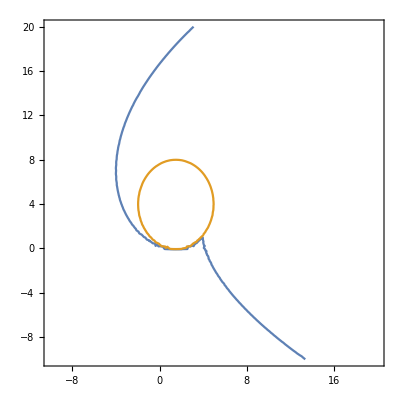

```mathematica
ContourPlot[{d==0,d0==0},{q1,-10,20},{q2,-10,20}]
```

```mathematica
Solve[{d==0,d0==0},{q1,q2}]//N
```

{{q2→0.},{q1→1.5,q2→0.},{q1→4.02375,q2→1.26001},{q1→-13.2619+6.23279 ⅈ,q2→11.37+16.6454 ⅈ},{q1→-13.2619-6.23279 ⅈ,q2→11.37-16.6454 ⅈ}}

#### Example 1 : Q (0, -1)

```mathematica
q={q1-> 0,q2-> -1}
```

{q1→0,q2→-1}

```mathematica
d/.q//N
```

5184.

```mathematica
NSolve[(gb[[1]]== 0)/.q,t,Reals]
```

{{t→-4.75877},{t→-0.305407},{t→2.06418}}

#### Example 2 : Q (-10, 5)

```mathematica
q={q1-> -10,q2-> 5}
```

{q1→-10,q2→5}

```mathematica
d/.q
```

78450000

```mathematica
NSolve[(gb[[1]]== 0)/.q,t,Reals]
```

{{t→-0.294163},{t→0.459992},{t→4.43417}}

## “Without Loss of Generality”

```mathematica
Clear[p1,p2,q1,q2,cm,cn,d,d0]
```

```mathematica
cubic=cm+p1+(cn+2 p2-q2) t+(cm-p1+2 q1) t^2+(cn+q2) t^3
```

cm+p1+(cn+2 p2-q2) t+(cm-p1+2 q1) t^2+(cn+q2) t^3

```mathematica
sols=Solve[{a== Coefficient[cubic,t,3],b== Coefficient[cubic,t,2],c== Coefficient[cubic,t,1],d== Coefficient[cubic,t,0]},{p1,p2,q1,q2}]
```

{{p1→-cm+d,p2→1/2 (a+c-2 cn),q1→1/2 (b-2 cm+d),q2→a-cn}}

```mathematica
sols/.{cm-> 0,cn-> 0,a-> 1,b-> -3,c-> 0,d-> 27/8}
```

{{p1→27/8,p2→1/2,q1→3/16,q2→1}}

```mathematica
sols/.{cm-> 0,cn-> 0,a-> 0,b-> -3,c-> 0,d-> 27/8}
```

{{p1→27/8,p2→0,q1→3/16,q2→0}}

### General equation a t^3 + b t^2 + c t + d = 0

```mathematica
Solve[{a== a0,b== b0,c== c0,d==d0},{p1,p2,q1,q2}]
```

{{p1→-cm+d0,p2→1/2 (a0+c0-2 cn),q1→1/2 (b0-2 cm+d0),q2→a0-cn}}

```mathematica
Solve[{a== 6,b== -2,c== 3/4,d==0},{p1,p2,q1,q2}]
```

{{p1→-cm,p2→27/8-cn,q1→-1-cm,q2→6-cn}}

```mathematica
Solve[{a== a0,b== 0,c== c0,d==0},{p1,p2,q1,q2}]
```

{{p1→-cm,p2→1/2 (a0+c0-2 cn),q1→-cm,q2→a0-cn}}

```mathematica
Solve[{a== 6,b== 0,c== 3/4,d==0},{p1,p2,q1,q2}]
```

{{p1→-cm,p2→27/8-cn,q1→-cm,q2→6-cn}}

```mathematica
Solve[6t^3+3/4t== 0,t]
```

{{t→0},{t→-ⅈ/(2 √2)},{t→ⅈ/(2 √2)}}

## The cusp point

```mathematica
P=OPoint[p1,p2];Q=OPoint[q1,q2];
```

```mathematica
m=OLine[1,0,cm];n=OLine[0,1,cn];
```

```mathematica
OMidPoint[P,Q]
```

OPoint[(p1+p2)/2,(q1+q2)/2]

```mathematica
circle1=ODistanceSq[OPoint[x,y],OMidPoint[P,Q]]-ODistanceSq[P,OMidPoint[P,Q]]
```

-(p1+1/2 (-p1-p2))^2-(p2+1/2 (-q1-q2))^2+(1/2 (-p1-p2)+x)^2+(1/2 (-q1-q2)+y)^2

```mathematica
circle2=ODistanceSq[OPoint[x,y],OPoint[0,0]]-ODistanceSq[P,Q]
```

-(p1-q1)^2-(p2-q2)^2+x^2+y^2

```mathematica
tgcircles=ODistanceSq[P,Q]-(ODistanceSq[P,OMidPoint[P,Q]]-ODistanceSq[P,Q])
```

-(p1+1/2 (-p1-p2))^2+2 (p1-q1)^2-(p2+1/2 (-q1-q2))^2+2 (p2-q2)^2

```mathematica
SonC1=circle1/.{x-> s1,y-> s2}
```

-(p1+1/2 (-p1-p2))^2-(p2+1/2 (-q1-q2))^2+(1/2 (-p1-p2)+s1)^2+(1/2 (-q1-q2)+s2)^2

```mathematica
SonC2=circle2/.{x-> s1,y-> s2}
```

-(p1-q1)^2-(p2-q2)^2+s1^2+s2^2

```mathematica
GroebnerBasis[{SonC1,SonC2,tgcircles}/.{p1-> 3,p2-> 4},{q1,q2},{s1,s2}]
```

{135-32 q1+7 q1^2-48 q2-2 q1 q2+7 q2^2}

```mathematica
poly=135-32 q1+7 q1^2-48 q2-2 q1 q2+7 q2^2
```

135-32 q1+7 q1^2-48 q2-2 q1 q2+7 q2^2

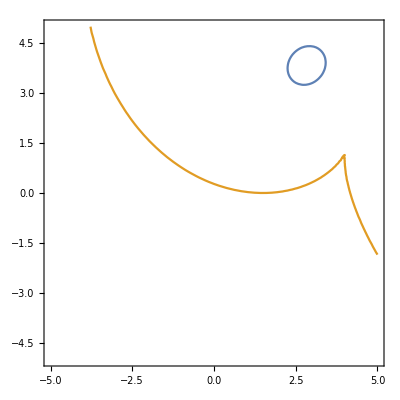

```mathematica
ContourPlot[{poly== 0,(225-354 q1+172 q1^2-24 q1^3-872 q2+264 q1 q2-16 q1^2 q2+174 q2^2-30 q1 q2^2+q1^2 q2^2-24 q2^3+q2^4)==0},{q1,-5,5},{q2,-5,5}]
```

```mathematica
f[x_,y_]:=(225-354 q1+172 q1^2-24 q1^3-872 q2+264 q1 q2-16 q1^2 q2+174 q2^2-30 q1 q2^2+q1^2 q2^2-24 q2^3+q2^4)/.{q1-> x,q2-> y}
```

```mathematica
F[x_,y_]:=D[f[x,y],x]
```

```mathematica
G[x_,y_]:=D[f[x,y],y]
```

```mathematica
s=Solve[{F[x,y]==0, G[x,y]==0},{x,y},Reals]//FullSimplify
```

{{x→3/2 (-5+3^(1/3)+3 3^(2/3)),y→8-9 3^(1/3)+3 3^(2/3)}}

#### Test

(O6) The fold that brings P onto m and Q onto n.

All parabola are similar. Without loss of generalization, take two perpendiculat lines m and n.

```mathematica
P=OPoint[3, 4];Q=OPoint[3/2 (-5+3^(1/3)+3 3^(2/3)),8-9 3^(1/3)+3 3^(2/3)];
```

```mathematica
m=OLine[1,0,0];n=OLine[0,1,0];
```

Equation of parabola (P, m)

```mathematica
parabolaeq1=ODistance[OPoint[x,y],P]^2-ODistanceSq[OPoint[x,y],m]
```

(-3+x)^2-x^2+(-4+y)^2

Equation of parabola (Q, n)

```mathematica
parabolaeq2=ODistance[OPoint[x,y],Q]^2-ODistanceSq[OPoint[x,y],n]
```

(-3/2 (-5+3^(1/3)+3 3^(2/3))+x)^2-y^2+(-8+9 3^(1/3)-3 3^(2/3)+y)^2

The equation of a tangent to parabola (P, m) and passing through point S(x1,y1)

```mathematica
tgparabola1=(D[parabolaeq1,x]/.{x-> x1, y-> y1})+ (D[parabolaeq1,y]/.{x-> x1, y-> y1})t
```

2 (-3+x1)-2 x1+2 t (-4+y1)

The equation of a tangent to parabola (Q, n) and passing through point T(x2,y2)

```mathematica
tgparabola2=(D[parabolaeq2,x]/.{x-> x2, y-> y2})+ (D[parabolaeq2,y]/.{x-> x2, y-> y2})t
```

2 (-3/2 (-5+3^(1/3)+3 3^(2/3))+x2)+t (-2 y2+2 (-8+9 3^(1/3)-3 3^(2/3)+y2))

Since the solution is common tangent to two parabolas, then tgparabola1 should also pass through T(x2, y2) and tgparabola2 should pass through S(x1,y1).

```mathematica
cst1=tgparabola1/.{x-> x2,y-> y2}
```

2 (-3+x1)-2 x1+2 t (-4+y1)

```mathematica
cst2=tgparabola2/.{x-> x1,y-> y1}
```

2 (-3/2 (-5+3^(1/3)+3 3^(2/3))+x2)+t (-2 y2+2 (-8+9 3^(1/3)-3 3^(2/3)+y2))

S(x1,y1) is a point of  parabola (P, m)

```mathematica
cst3=parabolaeq1/.{x-> x1,y-> y1}
```

(-3+x1)^2-x1^2+(-4+y1)^2

T(x2,y2) is a point of  parabola (Q, n)

```mathematica
cst4=parabolaeq2/.{x-> x2,y-> y2}
```

(-3/2 (-5+3^(1/3)+3 3^(2/3))+x2)^2-y2^2+(-8+9 3^(1/3)-3 3^(2/3)+y2)^2

Let t be the slope of the common tangent.

```mathematica
cst5=(y1-y2)-t(x1-x2)
```

-t (x1-x2)+y1-y2

```mathematica
gbx1=GroebnerBasis[{cst1==0,cst2==0,cst3== 0,cst4== 0,cst5== 0},{t},{x1,x2,y1,y2}]//FullSimplify
```

{-963384-3621213 3^(1/3)+2973951 3^(2/3)+t (37629198-11812005 3^(1/3)-9900255 3^(2/3)-3 (5962920-15843151 3^(1/3)+8118357 3^(2/3)) t+(-40198222+2155437 3^(1/3)+17830791 3^(2/3)) t^2)}

```mathematica
Collect[gbx1[[1]],{t,t^2,t^3}]
```

-963384-3621213 3^(1/3)+2973951 3^(2/3)+(37629198-11812005 3^(1/3)-9900255 3^(2/3)) t-3 (5962920-15843151 3^(1/3)+8118357 3^(2/3)) t^2+(-40198222+2155437 3^(1/3)+17830791 3^(2/3)) t^3

```mathematica
Solve[gbx1[[1]]== 0,{t}]
```

{{t→1/8 (-3-3^(1/3)-3 3^(2/3))},{t→1/8 (-3-3^(1/3)-3 3^(2/3))},{t→1/8 (-3-3^(1/3)-3 3^(2/3))}}

```mathematica
disc=4 (-(3-2 q1)^2 (-25+6 q1)-8 (109+q1 (-33+2 q1)) q2+(174+(-30+q1) q1) q2^2-24 q2^3+q2^4)
```

4 (-(3-2 q1)^2 (-25+6 q1)-8 (109+q1 (-33+2 q1)) q2+(174+(-30+q1) q1) q2^2-24 q2^3+q2^4)

### Proof

```mathematica
s
```

{{x→3/2 (-5+3^(1/3)+3 3^(2/3)),y→8-9 3^(1/3)+3 3^(2/3)}}

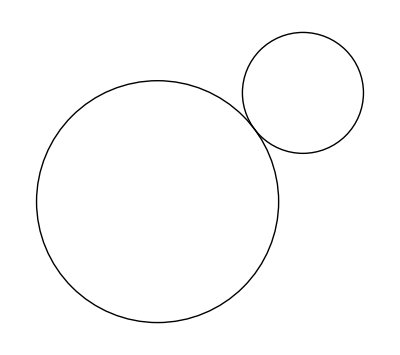

```mathematica
Graphics[{Circle[{(3+3/2 (-5+3^(1/3)+3 3^(2/3)))/2,(4+8-9 3^(1/3)+3 3^(2/3))/2},Sqrt[((3+3/2 (-5+3^(1/3)+3 3^(2/3)))/2-3)^2+((4+8-9 3^(1/3)+3 3^(2/3))/2-4)^2]], Circle[{0,0},Sqrt[(3/2 (-5+3^(1/3)+3 3^(2/3))-3)^2+(8-9 3^(1/3)+3 3^(2/3)-4)^2]]}]
```